#### Reif prob. 5.20 (0) Find the inversion curve for a van der waals gas.(1) Express your result in terms of the reduced variables p' and T', and find p' as a function of T' along the inversion curve. (2) Sketch this curve on a graph of p' versus T', being sure to indicate quantitatively the intercepts on the T' axis and the location of the maximum pressure on this curve

Before solve this problem, we have to solve 5.19

Van der waals gas : (p+a/v^2)(v-b)=R T

‘Critical point’ of van der waals gas : a point where (∂^2 p/∂v^2)_T=0  in addition to (∂p/∂v)_T=0

Temperature, pressure, molar volume of critical point: T_c, p_c, v_c

a. Express a,b in terms of T_c and v_c

```mathematica
p=(R T)/(v-b)-a/v^2;
firstder=D[(R T)/(v-b)-a/v^2,v]
```

(2 a)/v^3-(R T)/(-b+v)^2

```mathematica
seconder=D[(R T)/(v-b)-a/v^2,{v,2}]
```

-(6 a)/v^4+(2 R T)/(-b+v)^3

```mathematica
Solve[firstder==0&&seconder==0,{a,b}]
```

{{a→(9 R T v)/8,b→v/3}}

Therefore,  a=(9 R T_c v_c)/8 and   b=v_c/3 . Save these values in ‘abval’

```mathematica
abval=Solve[firstder==0&&seconder==0,{a,b}]
```

{{a→(9 R T v)/8,b→v/3}}

b. Express p_c in terms of T_c ,v_c

Replace !

```mathematica
p/.abval
```

{(3 R T)/(8 v)}

c.  Write the van der waals equation in terms of the reduced dimensionless variables

T'=T/T_c,   v'=v/v_c,    p'=p/p_c

(p+a v^-2)(v-b)=R T
(p+(9 R T_c v_c)/(8 v^2))(v-v_c/3)=R T
(p/p_c+(9 R T_c v_c)/(8 v^2) (8 v_c)/(3R T_c) )(v/v_c-1/3)=R T/(p_c v_c)
(p/p_c+(3 v_c^2)/v^2 )(v/v_c-1/3)=(8 v_c)/(3R T_c) (R T)/v_c
(p/p_c+(3 v_c^2)/v^2 )(v/v_c-1/3)=(8T)/(3 T_c)
(p'+3/v'^2 )(v'-1/3)=8/3 T'

Finally, we have  (p'+3/v'^2 )(v'-1/3)=8/3 T'  which involve neither a  nor  b

Now we are ready to solve 5.20

(0).  Inversion curve ; when  μ = v/c_p(T/v((∂ v)/(∂ T))_p-1)=0 → (∂v/∂T)_p=v/T

since  p is invariant,  d p=(∂p/∂T)_v dT+(∂p/∂v)_T dv=0

Recall that   p=(R T)/(v-b)-a/v^2

```mathematica
p=(R T)/(v-b)-a/v^2
```

-a/v^2+(R T)/(-b+v)

(∂p/∂T)_v is,

```mathematica
dpdt=D[p,T]
```

R/(-b+v)

(∂p/∂v)_T

```mathematica
dpdv=D[p,v]
```

(2 a)/v^3-(R T)/(-b+v)^2

((∂ v)/(∂ T))_p

```mathematica
dvdt=FullSimplify[-dpdt/dpdv]
```

(R v^3 (-b+v))/(-2 a (b-v)^2+R T v^3)

condition for inversion curve :  (∂v/∂T)_p=v/T

```mathematica
FullSimplify[dvdt==v/T]
```

(R v^3 (-b+v))/(-2 a (b-v)^2+R T v^3)==v/T

(1) Express this result in terms of the reduced variables  p' and T'

(R v^3 (-b+v))/(-2 a (b-v)^2+R T v^3)==v/T → (2a)/(R T)((v-b)/v)^2==b

(2a)/(R T)((v-b)/v)^2=b
2/(R T)9/8 R T_c(v_c((v-v_c/3)/v))^2=v_c/3 
9/4 (T_c/T)(1-v_c/(3v))^2=1/3  
(1-1/(3v'))^2=4/3 T'

eliminate v' and putting the equation in terms of  p' and T'

(note that  (p'+3/v'^2 )(v'-1/3)=8/3 T' )

```mathematica
Clear[p]
```

```mathematica
sol=Solve[(1-1/(3v))^2==4/3 t,v]
```

{{v→(-3-2 √3 √t)/(3 (-3+4 t))},{v→(-3+2 √3 √t)/(3 (-3+4 t))}}

```mathematica
sol=FullSimplify[sol]
```

{{v→1/(3-2 √3 √t)},{v→1/(3+2 √3 √t)}}

```mathematica
ptrela=((p+3/v^2)(v-1/3)==(8t)/3)/.sol
```

{(-1/3+1/(3-2 √3 √t)) (p+3 (3-2 √3 √t)^2)==(8 t)/3,(-1/3+1/(3+2 √3 √t)) (p+3 (3+2 √3 √t)^2)==(8 t)/3}

```mathematica
psol1=Simplify[Solve[ptrela[[1]],p]]
```

{{p→-27+40 √3 √t-44 t}}

```mathematica
psol2=FullSimplify[Solve[ptrela[[2]],p]]
```

{{p→-27-40 √3 √t-44 t}}

or,

```mathematica
Simplify[p/.Solve[(p+3/v^2)(v-1/3)==8/3 t,p]/.sol]
```

{{-27+40 √3 √t-44 t},{-27-40 √3 √t-44 t}}

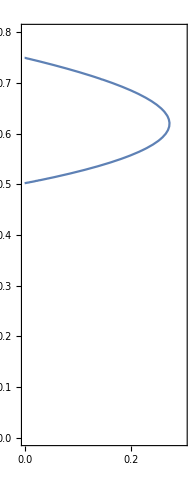

```mathematica
ContourPlot[-27+40 √3 √t-44 t==p,{p,0,0.3},{t,0,0.8},AspectRatio->Automatic]
```

Maximum & minimum temperature

```mathematica
Solve[-27+40 √3 √t-44 t==0,t]
```

{{t→243/484},{t→3/4}}

Temperature of maximum-pressure-point

```mathematica
Solve[D[-27+40 √3 √t-44 t,t]==0,t]
```

{{t→75/121}}

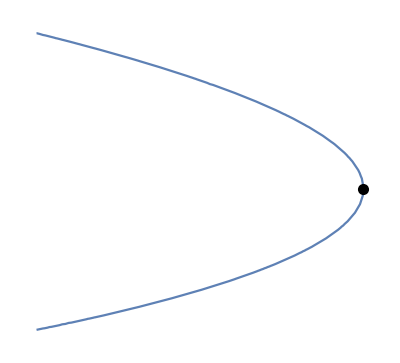

```mathematica
Show[{Graphics[{PointSize[0.02],Point[{-27+40 √3 √t-44 t/.t->75/121, 75/121}]}],ContourPlot[-27+40 √3 √t-44 t==p,{p,0,0.3},{t,0,0.8}]}]
```